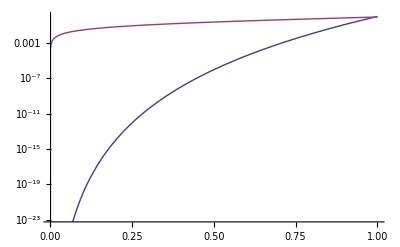

```mathematica
LogPlot[{x^20,(Exp[2x]-1)/Exp[2]},{x,0.001,1}]
```

```mathematica
expskew[vel_,skew_]:=(Exp[skew vel]-1)/(Exp[skew]-1)
```

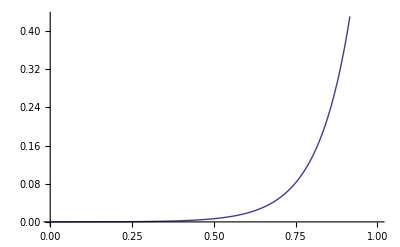

```mathematica
Plot[expskew[x,10],{x,0.001,1}]
```

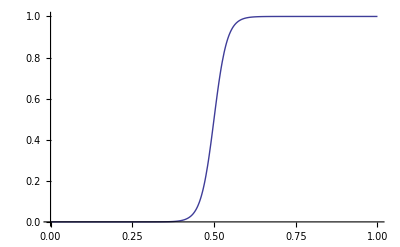

```mathematica
Plot[expskew[v1,50]/(expskew[.5,50]+expskew[v1,50]),{v1,0,1},PlotRange->All]
```

```mathematica
Erad[x_,y_,x0_,y0_]:=1/((x-x0)^2+(y-y0)^2)
```

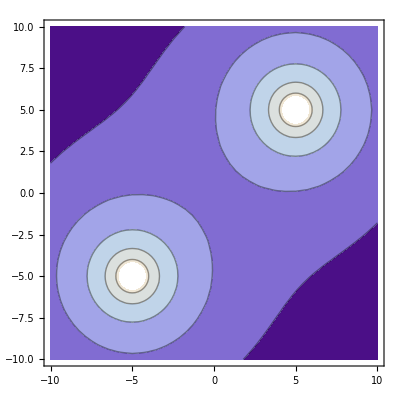

```mathematica
ContourPlot[Log[Erad[x,y,-5,-5]+Erad[x,y,5,5]],{x,-10,10},{y,-10,10}]
```